```mathematica
dataUpTo7=Import[FileNameJoin[{NotebookDirectory[],"data",ToString[#]<>"-points.csv"}]]&/@Range[1,7]
```

```mathematica
plotFacetVert[data_,dim_]:=Show[Plot[(2^(dim+1)×dim)/x,{x,1,2^(dim+1)},PlotRange->All,PlotStyle->{LightBlue,Dashed}],ListPlot[data,PlotStyle->{PointSize[0.01],Yellow},AxesOrigin->{0,0}],PlotRange->{{0,2^dim+2},{0,2^dim+2}},AspectRatio->1,AxesOrigin->{0,0},AxesStyle->{{Bold,White},{Bold,White}},AxesLabel->(Style[#,White,Background->Black]&/@{"Facets","Vertices"}),GridLines->Automatic,GridLinesStyle->Gray,Background->Black,PlotLabel->Style["Facets and vertices of 2-level polytopes in dim "<>ToString[dim],White,Background->Black],ImageSize->600]
```

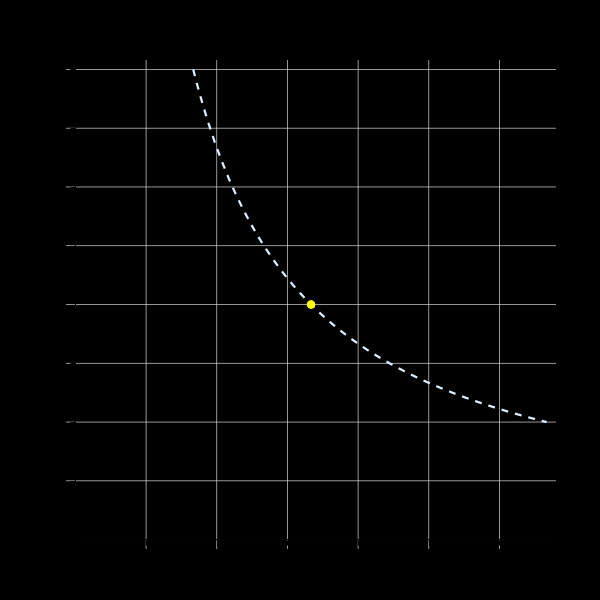
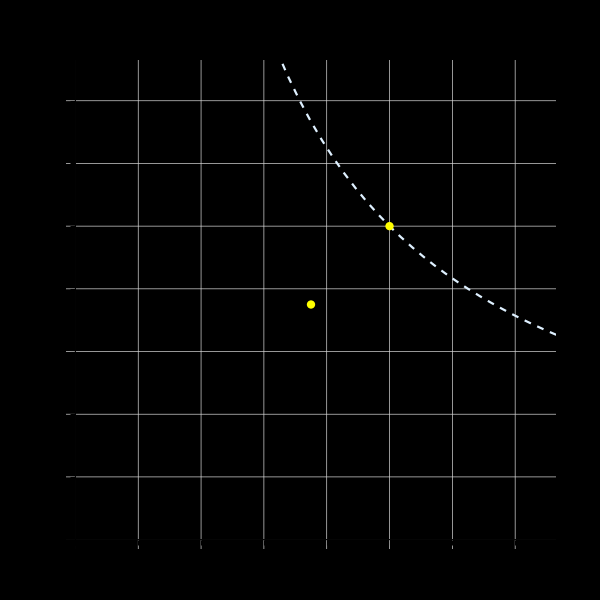
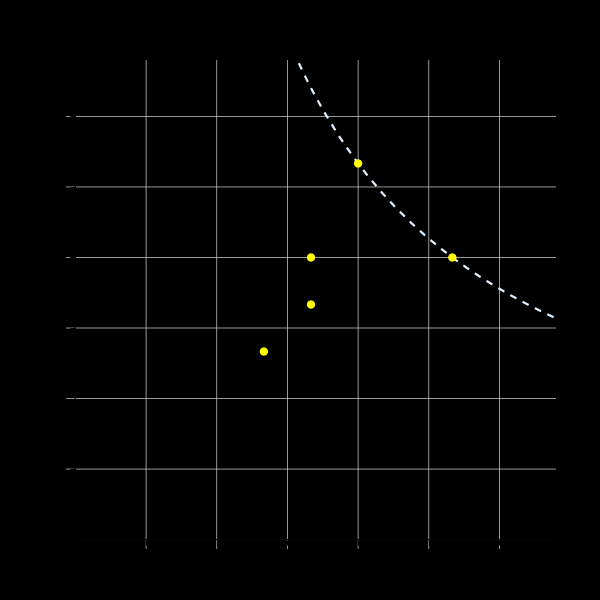
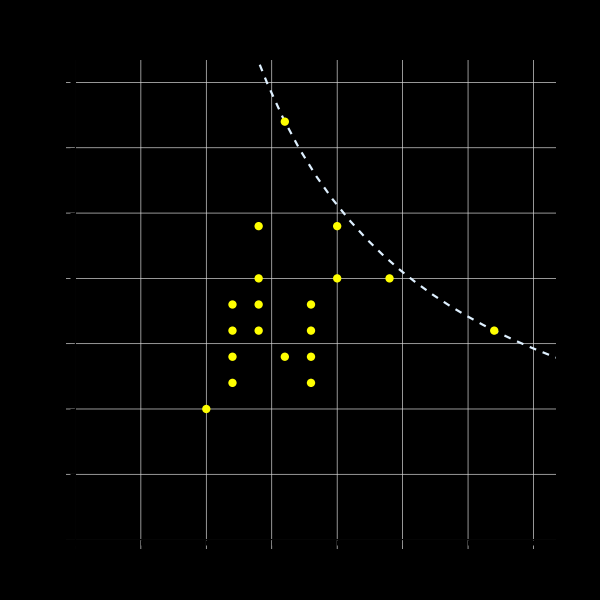
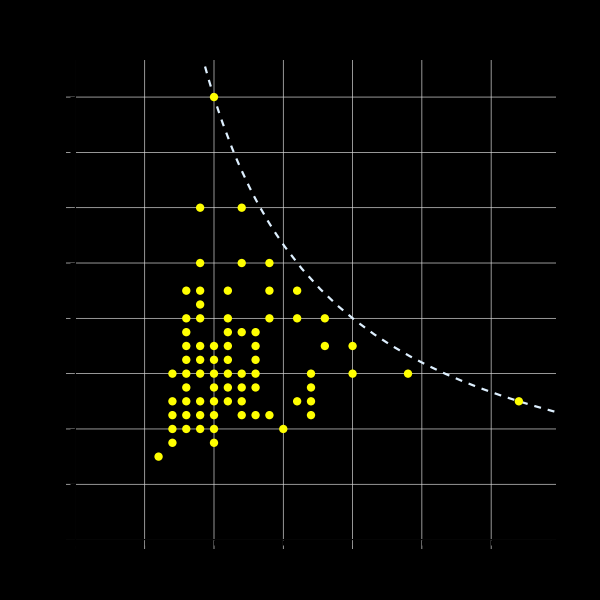
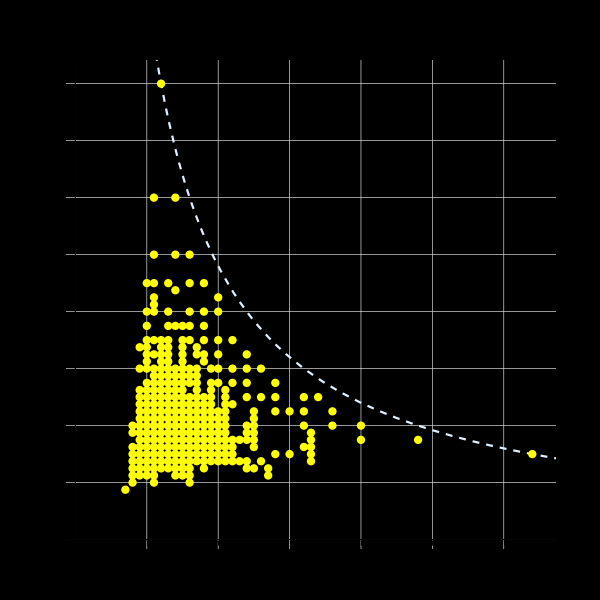
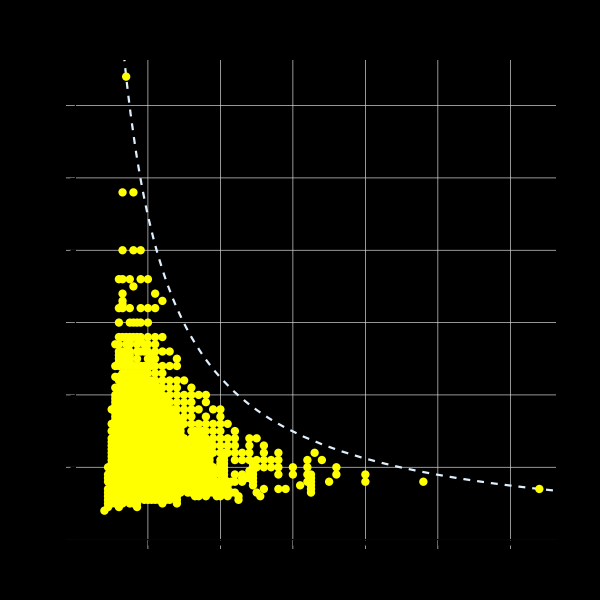
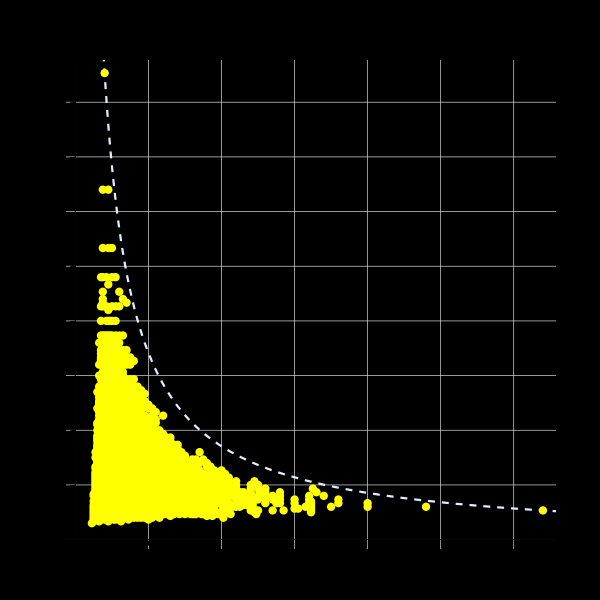

```mathematica
MapIndexed[plotFacetVert[#1,#2[[1]]]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-vert-facet-plots-"<>ToString[#2[[1]]]<>".jpg"}],#1]&,%];
```

```mathematica
points8=Import[FileNameJoin[{NotebookDirectory[],"data","8-points.csv"}]];
```

```mathematica
facetVertData=DeleteDuplicates/@Join[dataUpTo7,{points8}];
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"data","facet-vert-data-1to8.mx"}],facetVertData];
```

```mathematica
minProdData=DeleteDuplicates/@Map[{Min[#],#[[1]]#[[2]]}&,facetVertData,{2}];
maxProdData=DeleteDuplicates/@Map[{Max[#],#[[1]]#[[2]]}&,facetVertData,{2}];
```

```mathematica
vertProdData=DeleteDuplicates/@Map[{#[[2]],#[[1]]#[[2]]}&,facetVertData,{2}];
splitmaxProdData=DeleteDuplicates/@Map[{If[#[[1]]>#[[2]],#[[1]],-#[[2]]],#[[1]]#[[2]]}&,facetVertData,{2}];
```

```mathematica
fvdifProdData=Map[{#[[1]]-#[[2]],#[[1]]#[[2]]}&,facetVertData,{2}];
```

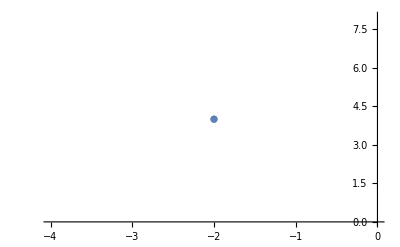
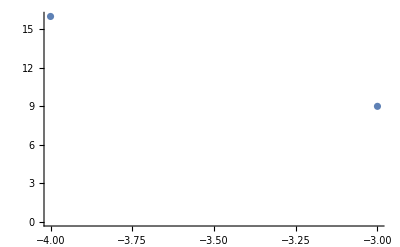
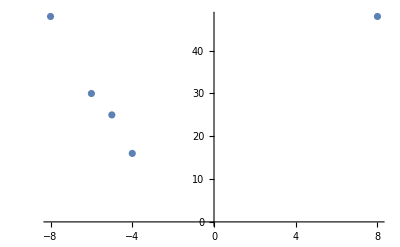
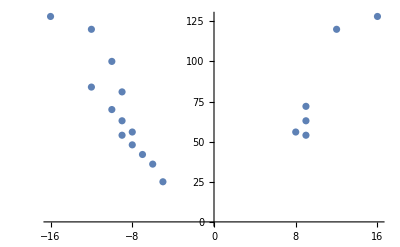
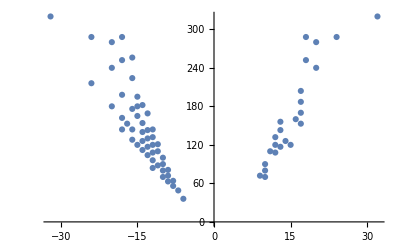
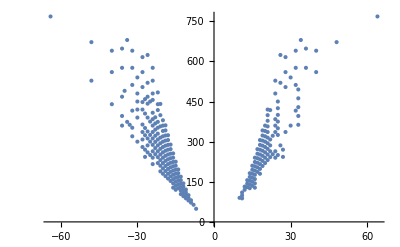
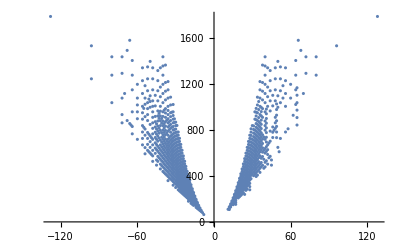
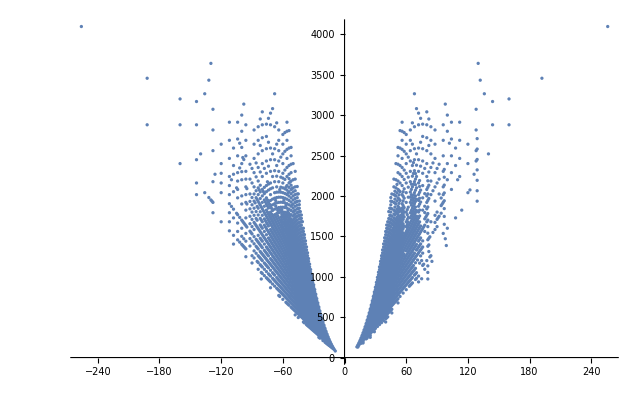

```mathematica
ListPlot[#,PlotRange->All,AxesOrigin->{0,0}]&/@splitmaxProdData
```

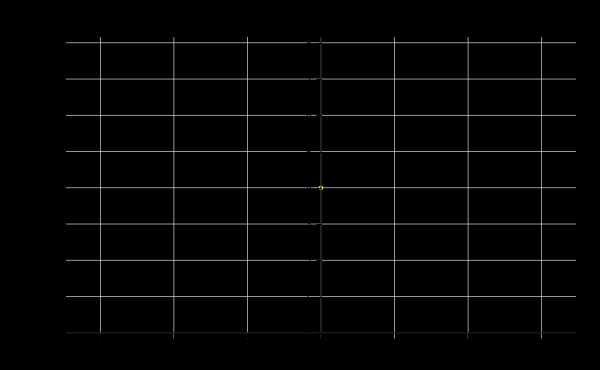
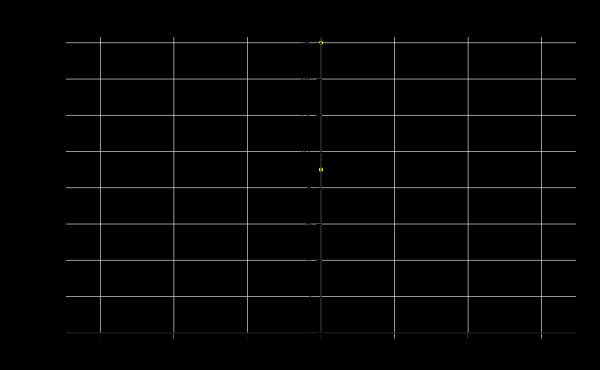
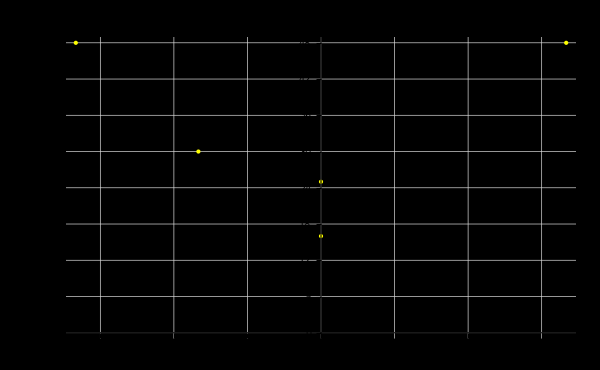
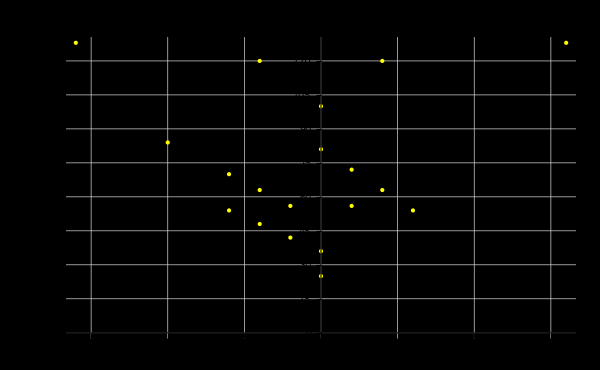
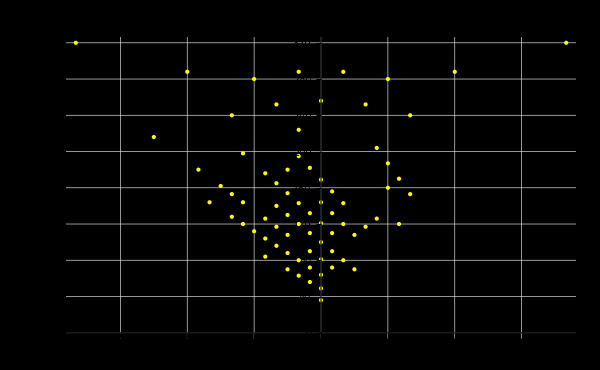
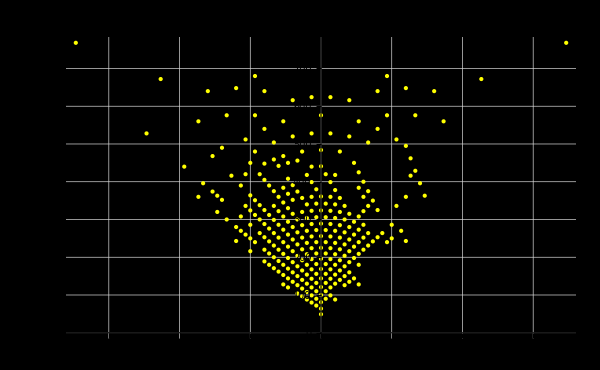
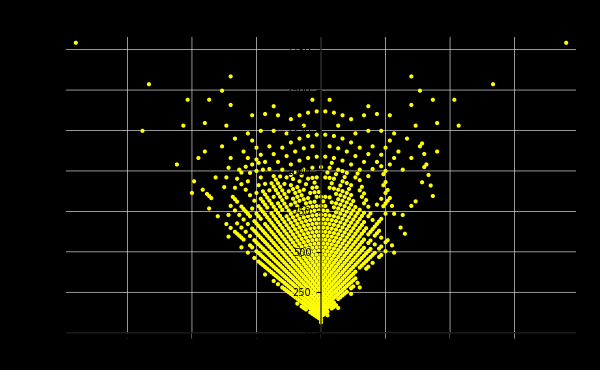
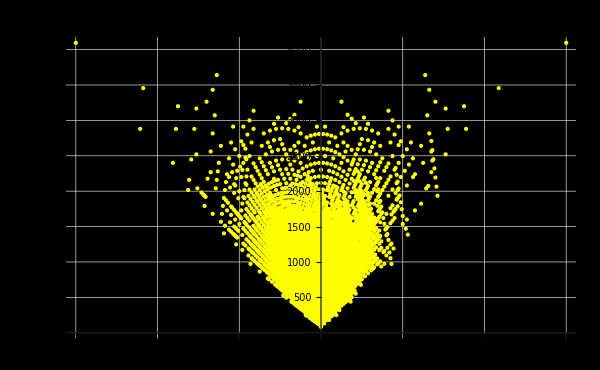
{-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{pt[[1]]-pt[[2]],Times@@pt},pt])/@#1,PlotRange->All,PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Difference vs Product in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"f·v"}],Style["f-v",White,Background->Black],Background->Black]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-dif-prod-plot-"<>ToString[#2[[1]]]<>".jpg"}],#1,Background->Black]&,%];
```

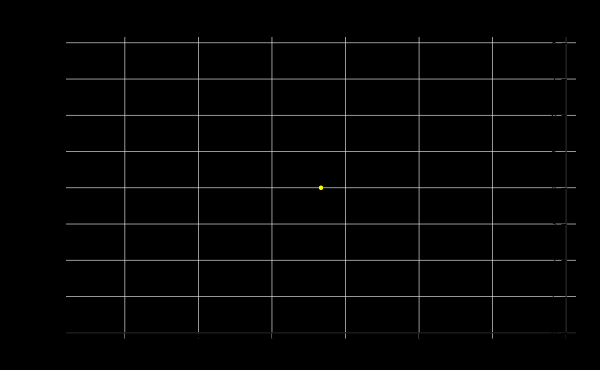
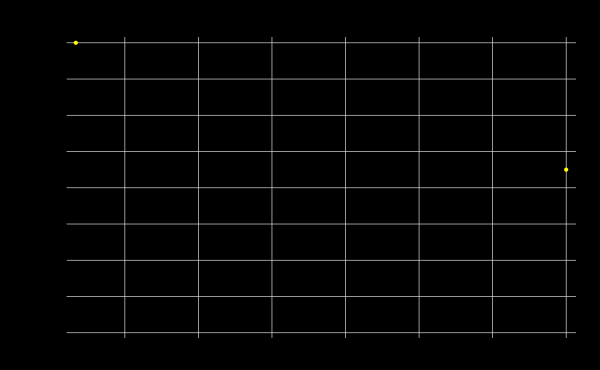
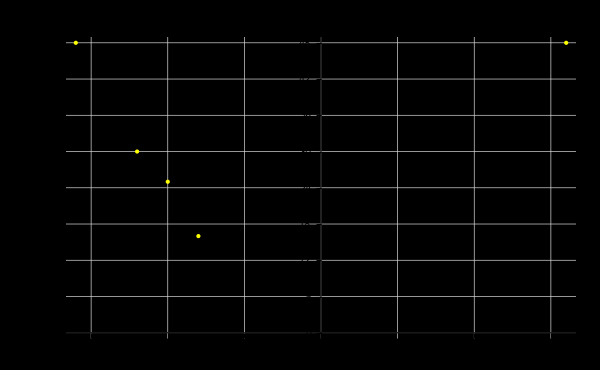
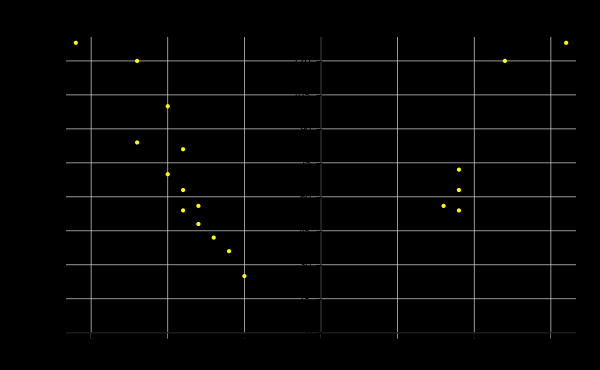
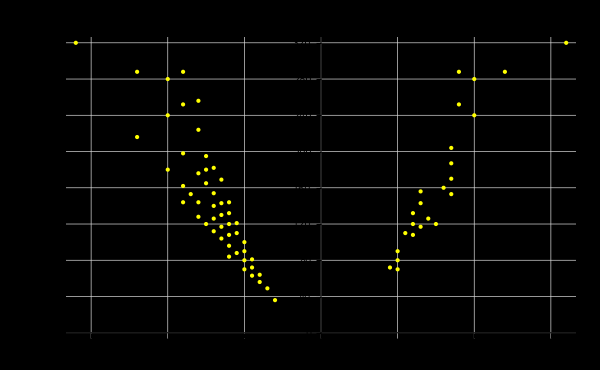
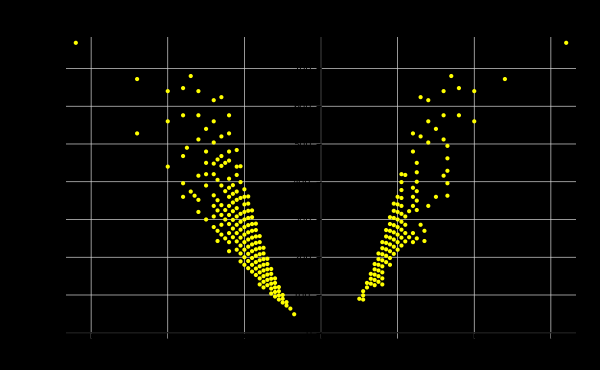
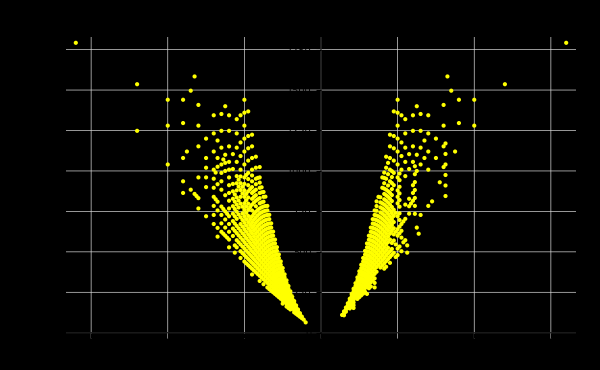
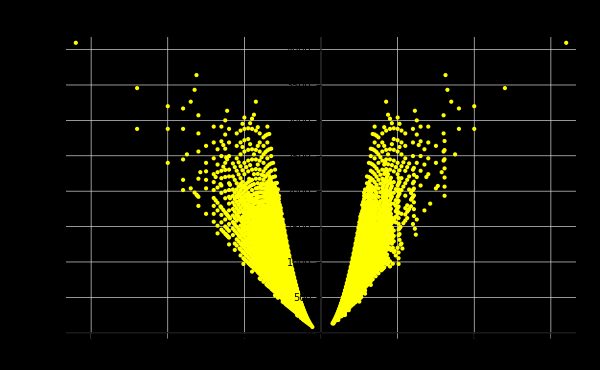
{-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{If[pt[[1]]>pt[[2]],pt[[1]],-pt[[2]]],Times@@pt},pt])/@#1,PlotRange->All,PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Max vs Product in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"f·v"}],Style["(-1)^(f > v)max(f,v)",White,Background->Black],Background->Black]&,facetVertData]
```